```mathematica
SetDirectory["/home/meike/Documents/"];
Get["PlotTheme.m"]
$PlotTheme="Publication";
Needs["ErrorBarPlots`"];
SetDirectory[]; 
path="/home/meike/Documents/literature/conferences/Elisbon/day07/exercise3/run09/";
```

```mathematica
settings=Import[path<>"settings.dat"]
tmax=settings[[1,2]];
dt=settings[[2,2]];
Ngrid=settings[[3,2]];
tprint=settings[[4,2]];
```

{{tmax,10},{dt,0.001},{N,100},{tprint,1},{lambda,10},{Pe,0.316228}}

```mathematica
{{"tmax",100},{"dt",0.01},{"N",100},{"tprint",10},{"lambda",0.1},{"Pe",3.16228}}
```

{{tmax,100},{dt,0.01},{N,100},{tprint,10},{lambda,0.1},{Pe,3.16228}}

```mathematica
tplus=IntegerPart[tprint/dt];
tmaxsteps=IntegerPart[tmax/dt];
gridt={};
mean={};
For[t = 0, t < tmaxsteps, t+=tplus, 
grid=Import[path<>"grid_t"<>ToString[t]<>".dat"];
AppendTo[gridt,grid];
AppendTo[mean,{t*dt,Mean[Flatten[grid]]}]
]
frame[t_]:=ListDensityPlot[gridt[[t]],ColorFunction->ColorData[{"RedBlueTones",{0,1}}],PlotLegends->Automatic,ImageSize->800]
```

```mathematica
Manipulate[ListDensityPlot[gridt[[step]],ColorFunction->ColorData[{"RedBlueTones",{0,1}}],PlotLegends->Automatic],{step,1,Length[gridt],1}]
```

Part::partw: Part 10 of {{{0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,«50»},«49»,«50»}} does not exist.

ListDensityPlot::arrayerr: {{{0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,«50»},«49»,«50»}}⟦10⟧ must be a valid array.

Part::partw: Part 10 of {{{0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,«50»},«49»,«50»}} does not exist.

ListDensityPlot::arrayerr: {{{0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,0.999921,«50»},«49»,«50»}}⟦10⟧ must be a valid array.

```mathematica
Integrate[(2Cos[x]Cos[y])/(2π)^2,{x,0,2π},{y,0,π/2}]
```

0

```mathematica
frames3=ParallelTable[frame[t],{t,1,Length[gridt],1}];
Export["/home/meike/day7_ex3_frames.avi",frames3]
```

/home/meike/day7_ex3_frames.avi

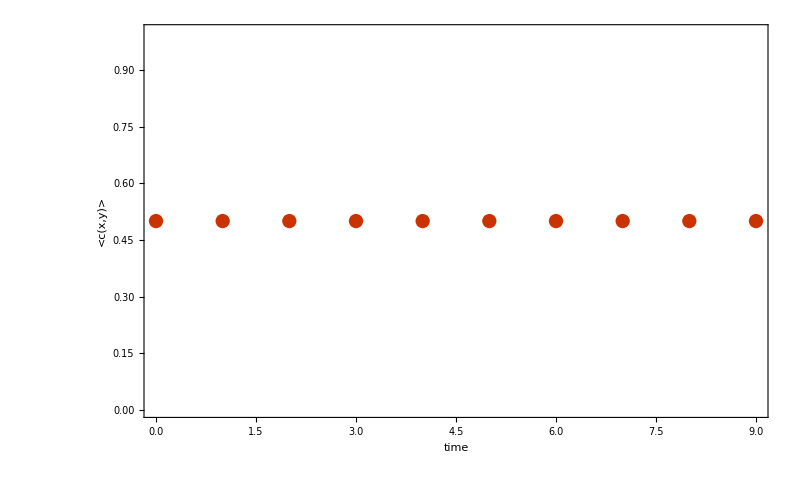

```mathematica
meanplot3=ListPlot[mean,FrameLabel->{"time","<c(x,y)>"},ImageSize->800,PlotRange->{0,1}]
```

```mathematica
Export["/home/meike/Dropbox/phd/figures/day7_ex3_mean.png",meanplot3]
```

/home/meike/Dropbox/phd/figures/day7_ex3_mean.png

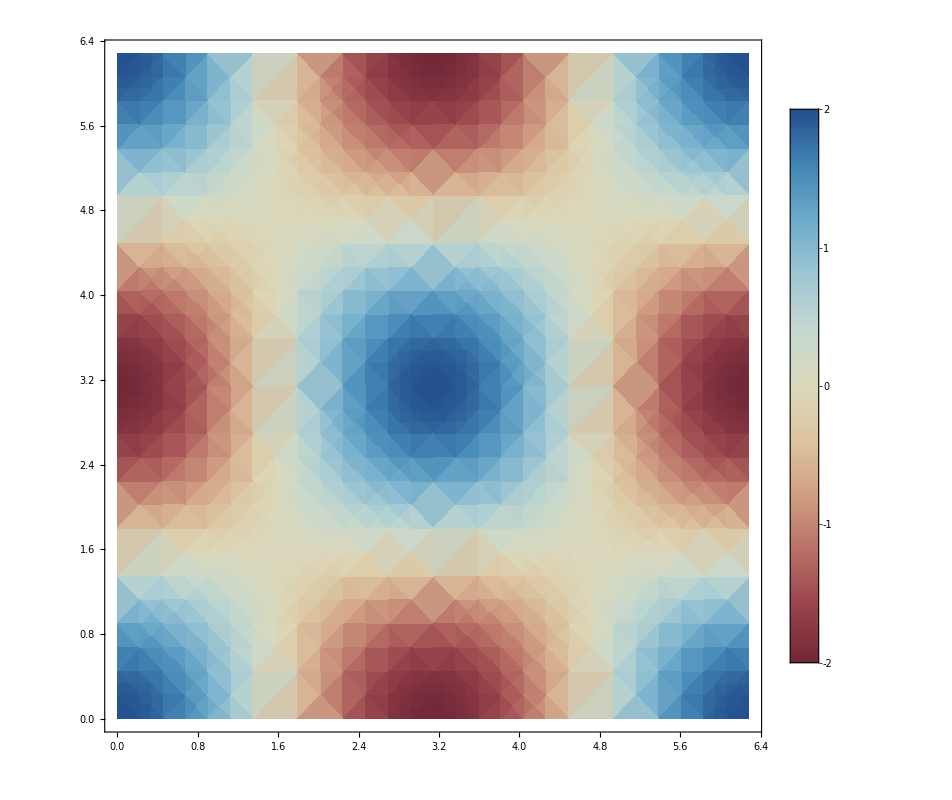

```mathematica
mplot=DensityPlot[2Cos[x]Cos[y],{x,0,2π},{y,0,2π},ColorFunction->ColorData[{"RedBlueTones",{0,1}}],PlotLegends->Automatic,ImageSize->800]
```

```mathematica
Export["/home/meike/Dropbox/phd/figures/day07_polarisation.png",mplot]
```

/home/meike/Dropbox/phd/figures/day07_polarisation.png